#### Calibration trace at YOKO=0mA, 6.3~6.6GHz, 5dBm 10us integration 50Kavg,100KHz step

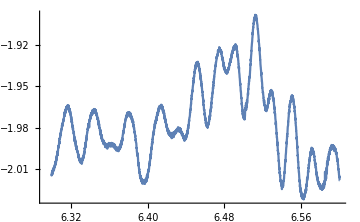
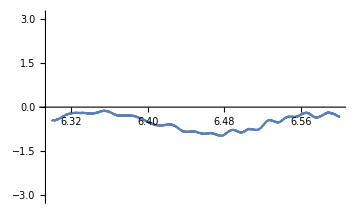

```mathematica
file="D:\\Travail Nath\\JQI\\branching_ratio_paper\\Data analysis package with 02 pumping\\one_tone_6.3GHz_to_6.6GHz_5dBm_0mA_10us integration_50Kavg_100KHz step_052518.dat";
data=Import[file];
header=Take[data,1];
ref=Drop[data,1];
edelay = 322.0;
ampref=ref[[;;,3]];
phaseref=ref[[;;,2]];
Row@{ListLinePlot[{#[[1]],Log10@#[[3]]}&/@ref,PlotRange->All,ImageSize->Medium],
ListLinePlot[{#[[1]],Arg[Exp[I(#[[2]]-edelay*#[[1]])]]}&/@ref,PlotRange->{-Pi,Pi},ImageSize->Medium]}
```

#### T2 echo of 0-1, after pumping 0-2(5dBm, 50us), 100Kavg_5us integration to 40us

{/demod_Magnitude0,/demod_Phase0,/t2_delays}

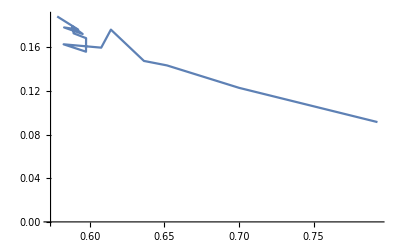

5.26796

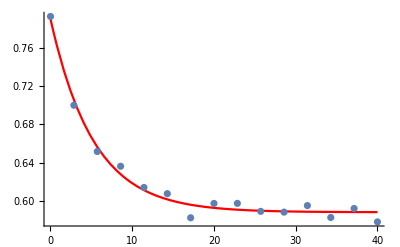

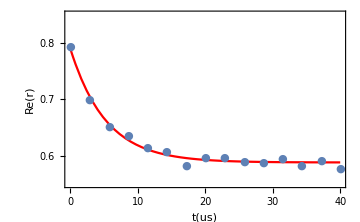

```mathematica
file="D:\\Travail Nath\\JQI\\branching_ratio_paper\\Data analysis package with 02 pumping\\061418_t2echo_pump_readout_6.4828GHz__-15dBm_qubit1.0105GHz_25dBm_detuning0GHZ_pump3.8366GHz_5dBm_-0.6_mA_100Kavg_5us integration.h5";(*"/Users/admin_ncottet/Documents/nc/JQI/branching_ratio_paper/Data analysis package with 02 pumping/061418_t2echo_pump_readout_6.4828GHz__-15dBm_qubit1.0105GHz_25dBm_detuning0GHZ_pump3.8366GHz_5dBm_-0.6_mA_100Kavg_5us integration.h5";*)
header=Import[file]
edelay = 322;
Freadout=6.4828;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset=0.65π/2;
powerRef=5;
refPoint=IntegerPart[1+(Freadout-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
amp=Flatten@Import[file,{"Datasets",1}];
phase=Flatten@Import[file,{"Datasets",2}];
refl=10^(-(powerReadout-powerRef)/20)*amp*Exp[I*(phase-edelay*Freadout+phaseoffset)]/ampref[[refPoint]];
ListLinePlot[Transpose@{Re[refl], Im[refl]}]
fit=FindFit[Transpose[{delays/1000,Re[refl]}][[;;]],A*Exp[-t/T2]+B,{{A,0.3},B,{T2,5}},t];
T2/.fit
Show[Plot[A*Exp[-t/T2]+B/.fit,{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Red,PlotRange->All],ListPlot[{Transpose@{delays/1000,Re[refl]}},PlotRange->All],PlotRange->All]
Show[Plot[A*Exp[-t/T2]+B/.fit,{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Red,PlotRange->{{0.0,40},{0.55,0.85}}],ListPlot[{Transpose@{delays/1000,Re[refl]}},PlotRange->{{0.0,40},{0.55,0.85}},PlotMarkers->{"●"}],PlotRange->{{0.0,40},{0.55,0.85}}, Frame->True,LabelStyle->Large,FrameLabel->{t[us],Re[r]},FrameTicks->{{Table[0.1i,{i,5,8}],None},{Table[10i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

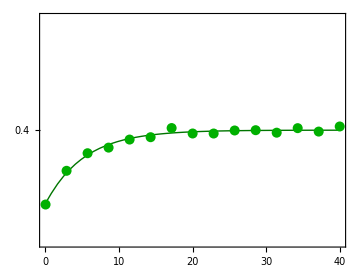

```mathematica
P0ini=0.64;
r0=0.658;
Show[Plot[(1-(A*Exp[-t/T2]+B))*(P0ini/r0)/.fit,{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[0,0.69,0],Thick],PlotRange->{0.1,.7}],ListPlot[{Transpose@{delays/1000,(1-Re[refl])*(P0ini/r0)}},PlotStyle->Directive[RGBColor[0,0.69,0],PointSize[0.02]]], Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[10i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

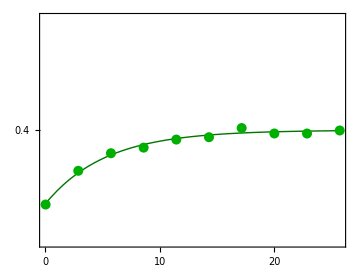

```mathematica
P0ini=0.64;
r0=0.658;
Show[Plot[(1-(A*Exp[-t/T2]+B))*(P0ini/r0)/.fit,{t,delays[[1]]/1000,delays[[10]]/1000},PlotStyle->Directive[Darker@RGBColor[0,0.69,0],Thick],PlotRange->{0.1,.7}],ListPlot[{Transpose@{delays[[;;10]]/1000,(1-Re[refl[[;;10]]])*(P0ini/r0)}},PlotStyle->Directive[RGBColor[0,0.69,0],PointSize[0.02]]], Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[10i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

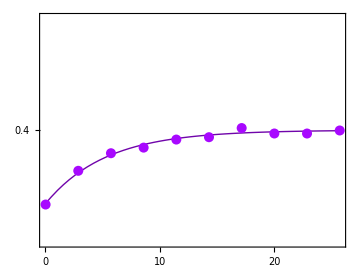

```mathematica
P0ini=0.64;
r0=0.658;
Show[Plot[(1-(A*Exp[-t/T2]+B))*(P0ini/r0)/.fit,{t,delays[[1]]/1000,delays[[10]]/1000},PlotStyle->Directive[Darker@RGBColor["#A808FF"],Thick],PlotRange->{0.1,.7}],ListPlot[{Transpose@{delays[[;;10]]/1000,(1-Re[refl[[;;10]]])*(P0ini/r0)}},PlotStyle->Directive[RGBColor["#A808FF"],PointSize[0.02]]], Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[10i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```